```mathematica
Quiet[Needs["HypExp`"]];
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
$HistoryLength=2;
turnOffConditional[];

$Assumptions=0<eps<1&&0≤u≤1&&0≤v≤1&&beta>0;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}]/.PlusDistribution[a_]:>HeavisideTheta[tau-beta]a+DiracDelta[tau-beta]Integrate[a,{tau,1,tau}];

replSymmPlus[e_]:=e/.ubar->1-u/.vbar->1-v/.PlusDistribution[HeavisideTheta[u-v]a_+HeavisideTheta[v-u]b_]:> HeavisideTheta[u-v-beta]a+HeavisideTheta[v-u-beta]b+DiracDelta[u-v-beta]Integrate[a/.u->w,{w,1,u},Assumptions->1>u>v+beta]-DiracDelta[v-u-beta]Integrate[b/.u->w,{w,0,u},Assumptions->1>v>u+beta]

anomDim2a1One=(alphaMS*DiracDelta[u-v]/Pi)(Cf*(LQ-3/2+Log[vbar])+(Ca/2)(5/2+Log[v/vbar]))
anomDim2a1Two=(alphaMS/Pi)(Cf-Ca/2)(1/(v*vbar^2))(u*v*(ubar*vbar+ubar+vbar-1)HeavisideTheta[1-u-v]+ubar^2*vbar^2HeavisideTheta[u+v-1] )
anomDim2a1Three=-(alphaMS/Pi)(Ca/2)(1/(v*vbar^2))(v*ubar^2*(1+vbar)HeavisideTheta[u-v]+u*vbar^2*(1+ubar)HeavisideTheta[v-u]+PlusDistribution[v*ubar^2HeavisideTheta[u-v]+u*vbar^2HeavisideTheta[v-u]])
anomDim2a1BetaThree=anomDim2a1Three//replSymmPlus
anomDim2a1=anomDim2a1One+anomDim2a1Two+anomDim2a1BetaThree

replDeltaForNIntegrate[e_]:=e/.DiracDelta[a_]:> HeavisideTheta[a+width/2]HeavisideTheta[width/2-a]/width/.width->1/25
```

(α_OverBar[MS] u-v (1/2 C_A (log(v/(v̄))+5/2)+C_F (LQ+log(v̄)-3/2)))/π

(α_OverBar[MS] (C_F-C_A/2) ((ū)^2 (v̄)^2 u+v-1+u v (ū v̄+ū+v̄-1) -u-v+1))/(π (v̄)^2 v)

-(C_A α_OverBar[MS] (((ū)^2 v u-v+(v̄)^2 u v-u)_++(ū)^2 (v̄+1) v u-v+(ū+1) (v̄)^2 u v-u))/(2 π (v̄)^2 v)

-(C_A α_OverBar[MS] (-((u^2 v^2)/2-u^2 v+u^2/2) u-v+β+((u^3 v)/3-u^2 v+u v-v/3) u-v-β+(1-u)^2 v u-v-β+u (1-v)^2 -u+v-β+(1-u)^2 (2-v) v u-v+(2-u) u (1-v)^2 v-u))/(2 π (1-v)^2 v)

(α_OverBar[MS] u-v (1/2 C_A (log(v/(v̄))+5/2)+C_F (LQ+log(v̄)-3/2)))/π-(C_A α_OverBar[MS] (-((u^2 v^2)/2-u^2 v+u^2/2) u-v+β+((u^3 v)/3-u^2 v+u v-v/3) u-v-β+(1-u)^2 v u-v-β+u (1-v)^2 -u+v-β+(1-u)^2 (2-v) v u-v+(2-u) u (1-v)^2 v-u))/(2 π (1-v)^2 v)+(α_OverBar[MS] (C_F-C_A/2) ((ū)^2 (v̄)^2 u+v-1+u v (ū v̄+ū+v̄-1) -u-v+1))/(π (v̄)^2 v)

#### Make sure we can integrate the anomalous dimensions

```mathematica
(anomDim2a1One/.u->U/.v->u/.U->v)/v/.ubar->1-u/.vbar->1-v
igralDelta=Integrate[%,{v,0,1}]
```

(α_OverBar[MS] v-u (1/2 C_A (log(u/(1-v))+5/2)+C_F (LQ+log(1-v)-3/2)))/(π v)

(1-u u α_OverBar[MS] (2 C_A log(-u/(u-1))+5 C_A+4 LQ C_F+4 C_F log(1-u)-6 C_F))/(4 π u)

```mathematica
(anomDim2a1Two/.u->U/.v->u/.U->v)/(v)/.ubar->1-u/.vbar->1-v//Expand
igrandTwo1=%/.HeavisideTheta[u+v-1]->0/.HeavisideTheta[-u-v+1]->1
igralTwo1=integrateTermByTerm[igrandTwo1,{v,0,1-u}]

(anomDim2a1Two/.u->U/.v->u/.U->v)/(v)/.ubar->1-u/.vbar->1-v//Expand
igrandTwo2=%/.HeavisideTheta[u+v-1]->1/.HeavisideTheta[-u-v+1]->0//Simplify
igralTwo2=integrateTermByTerm[igrandTwo2,{v,1-u,1}]
```

-(u v C_A α_OverBar[MS] -u-v+1)/(2 π (1-v)^2)+(v C_A α_OverBar[MS] -u-v+1)/(π (1-v)^2)+(u C_A α_OverBar[MS] -u-v+1)/(π (1-v)^2)-(C_A α_OverBar[MS] -u-v+1)/(π (1-v)^2)-(u v C_A α_OverBar[MS] u+v-1)/(2 π (1-v)^2)-(v C_A α_OverBar[MS] u+v-1)/(2 π u (1-v)^2)+(v C_A α_OverBar[MS] u+v-1)/(π (1-v)^2)-(u C_A α_OverBar[MS] u+v-1)/(2 π (1-v)^2 v)-(C_A α_OverBar[MS] u+v-1)/(2 π u (1-v)^2 v)+(C_A α_OverBar[MS] u+v-1)/(π (1-v)^2 v)+(u C_A α_OverBar[MS] u+v-1)/(π (1-v)^2)+(C_A α_OverBar[MS] u+v-1)/(π u (1-v)^2)-(2 C_A α_OverBar[MS] u+v-1)/(π (1-v)^2)+(u v C_F α_OverBar[MS] -u-v+1)/(π (1-v)^2)-(2 v C_F α_OverBar[MS] -u-v+1)/(π (1-v)^2)-(2 u C_F α_OverBar[MS] -u-v+1)/(π (1-v)^2)+(2 C_F α_OverBar[MS] -u-v+1)/(π (1-v)^2)+(u v C_F α_OverBar[MS] u+v-1)/(π (1-v)^2)+(v C_F α_OverBar[MS] u+v-1)/(π u (1-v)^2)-(2 v C_F α_OverBar[MS] u+v-1)/(π (1-v)^2)+(u C_F α_OverBar[MS] u+v-1)/(π (1-v)^2 v)+(C_F α_OverBar[MS] u+v-1)/(π u (1-v)^2 v)-(2 C_F α_OverBar[MS] u+v-1)/(π (1-v)^2 v)-(2 u C_F α_OverBar[MS] u+v-1)/(π (1-v)^2)-(2 C_F α_OverBar[MS] u+v-1)/(π u (1-v)^2)+(4 C_F α_OverBar[MS] u+v-1)/(π (1-v)^2)

-(u v C_A α_OverBar[MS])/(2 π (1-v)^2)+(u C_A α_OverBar[MS])/(π (1-v)^2)+(v C_A α_OverBar[MS])/(π (1-v)^2)-(C_A α_OverBar[MS])/(π (1-v)^2)+(u v C_F α_OverBar[MS])/(π (1-v)^2)-(2 u C_F α_OverBar[MS])/(π (1-v)^2)-(2 v C_F α_OverBar[MS])/(π (1-v)^2)+(2 C_F α_OverBar[MS])/(π (1-v)^2)

Integrating -(α_OverBar[MS] u v C_A)/(2 π (1-v)^2)+(α_OverBar[MS] v C_A)/(π (1-v)^2)+(α_OverBar[MS] u C_A)/(π (1-v)^2)-(α_OverBar[MS] C_A)/(π (1-v)^2)+(α_OverBar[MS] C_F u v)/(π (1-v)^2)-(2 α_OverBar[MS] C_F v)/(π (1-v)^2)-(2 α_OverBar[MS] C_F u)/(π (1-v)^2)+(2 α_OverBar[MS] C_F)/(π (1-v)^2)

Integrating 8 terms.

Term 1 : -(α_OverBar[MS] C_A)/(π (1-v)^2)

1 : (α_OverBar[MS] C_A (u-1))/(π u)

Term 2 : (2 α_OverBar[MS] C_F)/(π (1-v)^2)

2 : (2 α_OverBar[MS] C_F (1/u-1))/π

Term 3 : (α_OverBar[MS] C_A u)/(π (1-v)^2)

3 : -(α_OverBar[MS] C_A (u-1))/π

Term 4 : -(2 α_OverBar[MS] C_F u)/(π (1-v)^2)

4 : (2 α_OverBar[MS] C_F (u-1))/π

Term 5 : (α_OverBar[MS] C_A v)/(π (1-v)^2)

5 : (α_OverBar[MS] C_A (log(u)+1/u-1))/π

Term 6 : -(2 α_OverBar[MS] C_F v)/(π (1-v)^2)

6 : -(2 α_OverBar[MS] C_F (log(u)+1/u-1))/π

Term 7 : -(α_OverBar[MS] C_A u v)/(2 π (1-v)^2)

7 : -(α_OverBar[MS] C_A (log(u) u-u+1))/(2 π)

Term 8 : (α_OverBar[MS] C_F u v)/(π (1-v)^2)

8 : (α_OverBar[MS] C_F (log(u) u-u+1))/π

-((u-1) C_A α_OverBar[MS])/π+((u-1) C_A α_OverBar[MS])/(π u)+(C_A α_OverBar[MS] (1/u+log(u)-1))/π-(C_A α_OverBar[MS] (-u+u log(u)+1))/(2 π)+(2 (1/u-1) C_F α_OverBar[MS])/π+(2 (u-1) C_F α_OverBar[MS])/π-(2 C_F α_OverBar[MS] (1/u+log(u)-1))/π+(C_F α_OverBar[MS] (-u+u log(u)+1))/π

-(u v C_A α_OverBar[MS] -u-v+1)/(2 π (1-v)^2)+(v C_A α_OverBar[MS] -u-v+1)/(π (1-v)^2)+(u C_A α_OverBar[MS] -u-v+1)/(π (1-v)^2)-(C_A α_OverBar[MS] -u-v+1)/(π (1-v)^2)-(u v C_A α_OverBar[MS] u+v-1)/(2 π (1-v)^2)-(v C_A α_OverBar[MS] u+v-1)/(2 π u (1-v)^2)+(v C_A α_OverBar[MS] u+v-1)/(π (1-v)^2)-(u C_A α_OverBar[MS] u+v-1)/(2 π (1-v)^2 v)-(C_A α_OverBar[MS] u+v-1)/(2 π u (1-v)^2 v)+(C_A α_OverBar[MS] u+v-1)/(π (1-v)^2 v)+(u C_A α_OverBar[MS] u+v-1)/(π (1-v)^2)+(C_A α_OverBar[MS] u+v-1)/(π u (1-v)^2)-(2 C_A α_OverBar[MS] u+v-1)/(π (1-v)^2)+(u v C_F α_OverBar[MS] -u-v+1)/(π (1-v)^2)-(2 v C_F α_OverBar[MS] -u-v+1)/(π (1-v)^2)-(2 u C_F α_OverBar[MS] -u-v+1)/(π (1-v)^2)+(2 C_F α_OverBar[MS] -u-v+1)/(π (1-v)^2)+(u v C_F α_OverBar[MS] u+v-1)/(π (1-v)^2)+(v C_F α_OverBar[MS] u+v-1)/(π u (1-v)^2)-(2 v C_F α_OverBar[MS] u+v-1)/(π (1-v)^2)+(u C_F α_OverBar[MS] u+v-1)/(π (1-v)^2 v)+(C_F α_OverBar[MS] u+v-1)/(π u (1-v)^2 v)-(2 C_F α_OverBar[MS] u+v-1)/(π (1-v)^2 v)-(2 u C_F α_OverBar[MS] u+v-1)/(π (1-v)^2)-(2 C_F α_OverBar[MS] u+v-1)/(π u (1-v)^2)+(4 C_F α_OverBar[MS] u+v-1)/(π (1-v)^2)

-((u-1)^2 α_OverBar[MS] (C_A-2 C_F))/(2 π u v)

Integrating -(α_OverBar[MS] u C_A)/(2 π v)-(α_OverBar[MS] C_A)/(2 π u v)+(α_OverBar[MS] C_A)/(π v)+(α_OverBar[MS] C_F u)/(π v)+(α_OverBar[MS] C_F)/(π u v)-(2 α_OverBar[MS] C_F)/(π v)

Integrating 6 terms.

Term 1 : (α_OverBar[MS] C_A)/(π v)

1 : -(α_OverBar[MS] C_A log(1-u))/π

Term 2 : -(2 α_OverBar[MS] C_F)/(π v)

2 : (2 α_OverBar[MS] C_F log(1-u))/π

Term 3 : -(α_OverBar[MS] C_A)/(2 π u v)

3 : (α_OverBar[MS] C_A log(1-u))/(2 π u)

Term 4 : (α_OverBar[MS] C_F)/(π u v)

4 : -(α_OverBar[MS] C_F log(1-u))/(π u)

Term 5 : -(α_OverBar[MS] C_A u)/(2 π v)

5 : (α_OverBar[MS] C_A u log(1-u))/(2 π)

Term 6 : (α_OverBar[MS] C_F u)/(π v)

6 : -(α_OverBar[MS] C_F u log(1-u))/π

(u C_A α_OverBar[MS] log(1-u))/(2 π)+(C_A α_OverBar[MS] log(1-u))/(2 π u)-(C_A α_OverBar[MS] log(1-u))/π-(u C_F α_OverBar[MS] log(1-u))/π-(C_F α_OverBar[MS] log(1-u))/(π u)+(2 C_F α_OverBar[MS] log(1-u))/π

```mathematica
(anomDim2a1BetaThree/.u->U/.v->u/.U->v)/v/.ubar->1-u/.vbar->1-v
plusPart=%/.HeavisideTheta[u-v]->0/.HeavisideTheta[v-u]->0//Simplify
Integrate[%,{v,0,1},Assumptions->0<beta<1/10&&0<v<1]
igralPlusPart=Limit[%,beta->0]


(anomDim2a1BetaThree/.u->U/.v->u/.U->v)/v/.ubar->1-u/.vbar->1-v
thetaPart=%-plusPart//Expand

thetaPart1=thetaPart/.HeavisideTheta[u-v]->0/.HeavisideTheta[v-u]->1//Simplify
igralTheta1=Integrate[thetaPart1,{v,u,1},Assumptions->0<beta<1/10&&0<v<1]

thetaPart2=thetaPart/.HeavisideTheta[u-v]->1/.HeavisideTheta[v-u]->0//Simplify
igralTheta2=Integrate[thetaPart2,{v,0,u},Assumptions->0<beta<1/10&&0<v<1]
```

-(C_A α_OverBar[MS] (-((u^2 v^2)/2-u v^2+v^2/2) -u+v+β+((u v^3)/3-u v^2+u v-u/3) u-v+β+(1-u)^2 v u-v-β+u (1-v)^2 -u+v-β+(1-u)^2 (2-v) v u-v+(2-u) u (1-v)^2 v-u))/(2 π (1-u)^2 u v)

-(C_A α_OverBar[MS] (-1/2 (u-1)^2 v^2 -u+v+β+1/3 u (v-1)^3 u-v+β+u (v-1)^2 -u+v-β+(u-1)^2 v u-v-β))/(2 π (u-1)^2 u v)

(C_A α_OverBar[MS] (u (β+u-1) ((β-5) β+u^2+(2 β-5) u-2) -u-β+1-3 (β+u) ((Piecewise[{{-2 u log(u+β), u+β<1}, {0, True}}])+(u-1)^2 (u-β) u-β)))/(12 π (u-1)^2 u (β+u))

Piecewise[{{-(C_A α_OverBar[MS])/(4 π), u≥1}, {-(C_A α_OverBar[MS] (3 (u-1)^2 u u-u^3+6 u^2-3 u-6 u log(u)-2))/(12 π (u-1)^2 u), True}}]

-(C_A α_OverBar[MS] (-((u^2 v^2)/2-u v^2+v^2/2) -u+v+β+((u v^3)/3-u v^2+u v-u/3) u-v+β+(1-u)^2 v u-v-β+u (1-v)^2 -u+v-β+(1-u)^2 (2-v) v u-v+(2-u) u (1-v)^2 v-u))/(2 π (1-u)^2 u v)

-(α_OverBar[MS] C_A u-v+β v^2)/(6 π (1-u)^2)+(α_OverBar[MS] C_A u-v+β v^2)/(6 π (u-1)^2)+(α_OverBar[MS] C_A u-v+β v)/(2 π (1-u)^2)-(α_OverBar[MS] C_A u-v+β v)/(2 π (u-1)^2)+(α_OverBar[MS] C_A u -u+v+β v)/(4 π (1-u)^2)-(α_OverBar[MS] C_A u -u+v+β v)/(4 π (u-1)^2)+(α_OverBar[MS] C_A -u+v+β v)/(4 π (1-u)^2 u)-(α_OverBar[MS] C_A -u+v+β v)/(4 π (u-1)^2 u)-(α_OverBar[MS] C_A -u+v+β v)/(2 π (1-u)^2)+(α_OverBar[MS] C_A -u+v+β v)/(2 π (u-1)^2)+(α_OverBar[MS] C_A u u-v v)/(2 π (1-u)^2)+(α_OverBar[MS] C_A u-v v)/(2 π (1-u)^2 u)-(α_OverBar[MS] C_A u-v v)/(π (1-u)^2)+(α_OverBar[MS] C_A u v-u v)/(2 π (1-u)^2)-(α_OverBar[MS] C_A v-u v)/(π (1-u)^2)-(α_OverBar[MS] C_A -u+v-β v)/(2 π (1-u)^2)+(α_OverBar[MS] C_A -u+v-β v)/(2 π (u-1)^2)-(α_OverBar[MS] C_A u-v+β)/(2 π (1-u)^2)+(α_OverBar[MS] C_A u-v+β)/(2 π (u-1)^2)-(α_OverBar[MS] C_A u u-v)/(π (1-u)^2)-(α_OverBar[MS] C_A u-v)/(π (1-u)^2 u)+(2 α_OverBar[MS] C_A u-v)/(π (1-u)^2)-(α_OverBar[MS] C_A u v-u)/(π (1-u)^2)+(2 α_OverBar[MS] C_A v-u)/(π (1-u)^2)-(α_OverBar[MS] C_A u u-v-β)/(2 π (1-u)^2)+(α_OverBar[MS] C_A u u-v-β)/(2 π (u-1)^2)-(α_OverBar[MS] C_A u-v-β)/(2 π (1-u)^2 u)+(α_OverBar[MS] C_A u-v-β)/(2 π (u-1)^2 u)+(α_OverBar[MS] C_A u-v-β)/(π (1-u)^2)-(α_OverBar[MS] C_A u-v-β)/(π (u-1)^2)+(α_OverBar[MS] C_A -u+v-β)/(π (1-u)^2)-(α_OverBar[MS] C_A -u+v-β)/(π (u-1)^2)+(α_OverBar[MS] C_A u-v+β)/(6 π (1-u)^2 v)-(α_OverBar[MS] C_A u-v+β)/(6 π (u-1)^2 v)+(α_OverBar[MS] C_A u v-u)/(2 π (1-u)^2 v)-(α_OverBar[MS] C_A v-u)/(π (1-u)^2 v)-(α_OverBar[MS] C_A -u+v-β)/(2 π (1-u)^2 v)+(α_OverBar[MS] C_A -u+v-β)/(2 π (u-1)^2 v)

((u-2) (v-1)^2 C_A α_OverBar[MS])/(2 π (u-1)^2 v)

-((u-2) C_A α_OverBar[MS] ((Piecewise[{{2 log(u), 0<u<1}, {0, True}}])+u^2-4 u+3))/(4 π (u-1)^2)

((v-2) C_A α_OverBar[MS])/(2 π u)

(u C_A α_OverBar[MS])/(4 π)-(C_A α_OverBar[MS])/π

```mathematica
FullSimplify[igralDelta+igralTwo1+igralTwo2+igralPlusPart+igralTheta1+igralTheta2,Assumptions->0<u<1]
linearGamma=%*u
```

(α_OverBar[MS] (-(u-1) ((u (2 u (3 u-5)-1)+17) C_A-6 (u-1) C_F (2 LQ+2 (u-1) u-3))+12 u tanh^-1(1-2 u) (u ((u-4) u+6) C_A-2 (u-2) (u-1)^2 C_F)+6 C_A ((u-1)^2 log(-u/(u-1))+(1-4 u) log(1-u)+5 u log(u))))/(12 π (u-1)^2 u)

(α_OverBar[MS] (-(u-1) ((u (2 u (3 u-5)-1)+17) C_A-6 (u-1) C_F (2 LQ+2 (u-1) u-3))+12 u tanh^-1(1-2 u) (u ((u-4) u+6) C_A-2 (u-2) (u-1)^2 C_F)+6 C_A ((u-1)^2 log(-u/(u-1))+(1-4 u) log(1-u)+5 u log(u))))/(12 π (u-1)^2)

(α_OverBar[MS] (-(u-1) ((u (2 u (3 u-5)-1)+17) C_A-6 (u-1) C_F (2 LQ+2 (u-1) u-3))+6 u (log(2-2 u)-log(2 u)) (u ((u-4) u+6) C_A-2 (u-2) (u-1)^2 C_F)+6 C_A ((u-1)^2 log(-u/(u-1))+(1-4 u) log(1-u)+5 u log(u))))/(12 π (u-1)^2)

(α_OverBar[MS] (ū ((u (2 u (3 u-5)-1)+17) C_A+6 ū C_F (2 LQ-2 ū u-3))+6 u (log(2 ū)-log(2 u)) (u ((u-4) u+6) C_A-2 (ū)^2 (u-2) C_F)+6 C_A ((ū)^2 log(u/(ū))+(1-4 u) log(ū)+5 u log(u))))/(12 π (ū)^2)

(α_OverBar[MS] (ū ((u (2 u (3 u-5)-1)+17) C_A-6 ū C_F (-2 LQ+2 ū u+3))+6 u log((ū)/u) (u ((u-4) u+6) C_A-2 (ū)^2 (u-2) C_F)+6 C_A ((ū)^2 log(u/(ū))-4 u log(ū)+log(ū)+5 u log(u))))/(12 π (ū)^2)

(C_A α_OverBar[MS] log(ū))/(2 π (ū)^2)+(u^4 C_A α_OverBar[MS] log((ū)/u))/(2 π (ū)^2)-(2 u^3 C_A α_OverBar[MS] log((ū)/u))/(π (ū)^2)+(3 u^2 C_A α_OverBar[MS] log((ū)/u))/(π (ū)^2)+(5 u C_A α_OverBar[MS] log(u))/(2 π (ū)^2)-(2 u C_A α_OverBar[MS] log(ū))/(π (ū)^2)+(17 C_A α_OverBar[MS])/(12 π ū)+(u^3 C_A α_OverBar[MS])/(2 π ū)-(5 u^2 C_A α_OverBar[MS])/(6 π ū)-(u C_A α_OverBar[MS])/(12 π ū)+(C_A α_OverBar[MS] log(u/(ū)))/(2 π)+(LQ C_F α_OverBar[MS])/π-(3 C_F α_OverBar[MS])/(2 π)-(u^2 C_F α_OverBar[MS] log((ū)/u))/π-(ū u C_F α_OverBar[MS])/π+(2 u C_F α_OverBar[MS] log((ū)/u))/π

(3 u^4 log((1-u)/u))/(2 π (1-u)^2)+(3 u^3)/(2 π (1-u))-(6 u^3 log((1-u)/u))/(π (1-u)^2)-(5 u^2)/(2 π (1-u))+(9 u^2 log((1-u)/u))/(π (1-u)^2)-(4 u^2 log((1-u)/u))/(3 π)-(4 (1-u) u)/(3 π)-u/(4 π (1-u))+17/(4 π (1-u))-(6 u log(1-u))/(π (1-u)^2)+(8 u log((1-u)/u))/(3 π)+(15 u log(u))/(2 π (1-u)^2)+(3 log(1-u))/(2 π (1-u)^2)+(3 log(u/(1-u)))/(2 π)-2/π

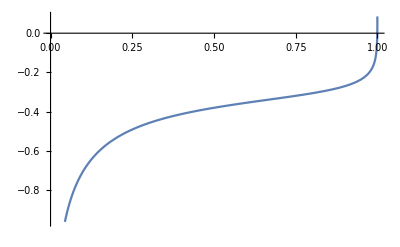

Plot::nonopt: Options expected (instead of TraditionalForm`{t, 0, 1}) beyond position TraditionalForm`2 in TraditionalForm`Plot[%/. u → t, Null, {t, 0, 1}]. An option must be a rule or a list of rules.

Plot[%/.u→t,Null,{t,0,1}]

Plot::nonopt: Options expected (instead of TraditionalForm`{t, 0, 1}) beyond position TraditionalForm`2 in TraditionalForm`Plot[%/. u → t, Null, {t, 0, 1}]. An option must be a rule or a list of rules.

Plot[%/.u→t,Null,{t,0,1}]

```mathematica
linearGamma//TrigToExp
%/. 1-u->ubar/.u-1->-ubar/. 2-2u->2ubar
FullSimplify[%,Assumptions->0<u<1&&0<ubar<1]
%//Expand

%/.Ca->3/.Cf->4/3/.alphaMS->1/.ubar->1-u/.LQ->0
Plot[%/.u->t,{t,0,1}]
```

{{Cc(u)→InterpolatingFunction[{{10., 1000.}}, <>](u),aa(u)→InterpolatingFunction[{{10., 1000.}}, <>](u)}}

InterpolatingFunction[{{10., 1000.}}, <>](u)

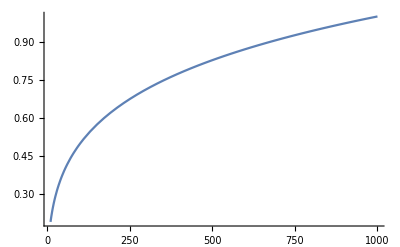

```mathematica
soln=NDSolve[{u*D[Cc[u],u]==3aa[u]Cc[u],u*D[aa[u],u]== -(11-2*5/3)aa[u]^2/(2*Pi),aa[91]== 0.118,Cc[1000]== 1},{Cc[u],aa[u]},{u,10,1000}]
(Cc[u]/.soln)[[1]]
Plot[Evaluate[(Cc[u]/.soln)],{u,10,1000}]
```

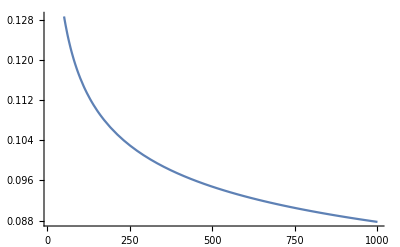

```mathematica
Plot[Evaluate[(aa[u]/.soln)],{u,10,1000}]
```

```mathematica
gammaTest[mu_,u_,v_]:=aa[mu]UnitStep[u-v]u*v
soln2=NDSolve[{mu*D[Cc[mu,u],mu]==Integrate[Cc[mu,v]*gammaTest[mu,v,u],{v,0,1},Assumptions->0<u<1],u*D[aa[u],u]== -(11-2*5/3)aa[u]^2/(2*Pi),aa[91]== 0.118,Cc[1000,u]== 1/u,D[Cc[mu,u],mu]/.mu->1000==-3},{Cc[mu,u],aa[u]},{u,10,1000}]
```

NDSolve::deqn: Equation or list of equations expected instead of TraditionalForm` in the first argument TraditionalForm`.

NDSolve[{mu Cc^(1,0)(mu,u)==Integrate[u v aa(mu) v-u Cc(mu,v),{v,0,1},Assumptions→0<u<1],u aa'(u)==-(23 (aa(u))^2)/(6 π),aa(91)==0.118,Cc(1000,u)==1/u,Cc^(1,0)(False,u)},{Cc(mu,u),aa(u)},{u,10,1000}]

```mathematica
Plot[%,]
```